# Lab: Euler’s Method

## Euler’s Method

Euler’s Method is a procedure to determine a numerical (or computational) solution to a first-order ordinary differential equation initial value problem.  Consider the following ODE:

dy/dt=f(t,y)
y(t_0)=y_0	(1)

Euler’s Method: Use the following recursive formulas to create a list of points approximating the solution to (1) for a step size h:

t_(n+1)=t_0+n h (difference between each x)
y_(n+1)=y_n+h f(t_n,y_n)→ slope between two points

## Part 1: Using Euler’s Method on dy/dt=5y, y(0)=1

Consider the following IVP:

dy/dt=5y
y(0)=1	(2)

(a) Use Euler’s Method to find a numerical solution to (2) on [0,1] with step size h=0.5.
(0,1)
(0.5,3.5)
(1,12.25)

```mathematica
Solve[y==3.5+(5*3.5)*.5,y]
```

{{y→12.25}}

(b) Use Euler’s Method to find a numerical solution to (2) on [0,1] with step size h=0.2.
(0 , 1)
(0.2 , 2)
(0.4 , 4)
(0.6 , 8)
(0.8 , 16)
(1 , 32)

```mathematica
Solve[y==16+5*16*.2,y]
```

{{y→32.}}

(c) Find an explicit solution to (2).  Check your answer in Mathematica with DSolve[ ].
∫dy/y = ∫5dt
ln(y) = 5t + c
e^ln(y) = e^(5t+c)
y = Ce^5t
1=C*e^0
1=C

```mathematica
y[t_]=E^(5t)
```

ⅇ^(5 t)

```mathematica
DSolve[y'[t]==5*y[t],y[t],t]
```

{{y[t]→ⅇ^(5 t) C[1]}}

(d) Plot the two numerical solutions and the explicit solution to (2) together on one graph.  Label your graph well.

```mathematica
plot1= ListPlot[{{0,1},{.5,3.5},{1,12.25}}, PlotStyle->Red, Joined->True,Mesh->All];
plot3= ListPlot[{{0,1},{.2,2},{.4,4},{.6,8},{.8,16},{1,32}}, PlotStyle->Blue, Joined->True,Mesh->All];
plot2=Plot[y[t],{t,0,5},PlotStyle->Green];
Show[plot1,plot2,plot3, PlotRange->{{0,1.5},{0,36}}]
```

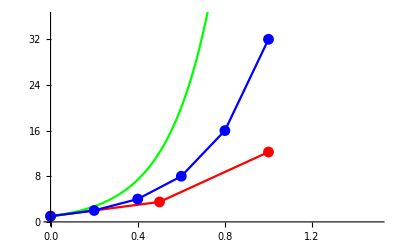

The green line is the function y(t)=e^(5t)
The blue line is the line from part 2- with the step size of .2
The red line is the line from part 1- with the step size of .5

## Part 2: Using Euler’s Method on dy/dt=y cos(t)+1, y(0)=2

Pick specific IVP that we need to solve numerically

Consider the following IVP:

dy/dt=y cos(t)+1
y(0)=2	(3)

(a) Use Euler’s Method to find a numerical solution to (3) on [0,10] with step size h=0.5.

{{0,2},{0,3.5},{0.5,5.53577},{1.,7.53126},{1.5,8.29763},{2.,7.07112},{2.5,4.73863},{3.,2.89302},{3.5,2.03843},{4.,1.87223},{4.5,2.1749},{5.,2.98336},{5.5,4.54048},{6.,7.22029},{6.5,11.2459},{7.,15.9851},{7.5,19.2556},{8.,18.3547},{8.5,13.3298},{9.,7.75723},{9.5,4.38958}}

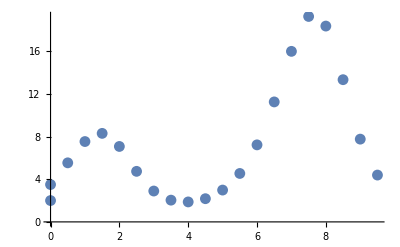

```mathematica
initialt=0;
finalt = 10;
t1=0;
y1=2;
h=0.5;
pointList = {{t1,y1}};

For[t=initialt, t<finalt,

y=y1+(y1* Cos[t] + 1)*(h);
t11=t;
y11=y;
pointList = Append[pointList,{t11,y11}];
t=t+h;
t1=t11;
y1=y11;
]
pointList
newPoints = ListPlot[pointList,PlotRange-> All]
```

(b) Use Euler’s Method to find a numerical solution to (3) on [0,10] with step size h=0.1.

(c) Use NDSolve[ ] to find an additional numerical solution to (3) on [0,10].

(d) Plot the three numerical solutions to (3) together on one graph.  Label your graph well.

## Part 3: Comparing Results and Discussion

(a) How does h (in general) affect the accuracy of numerical solutions using Euler’s Method?

(b) On which problem (from Part 1 or Part 2) did Euler’s Method seem to work better?  Why?

(c) What characteristics of the ODE or IVP would you expect to lead to good results using Euler’s Method?  Which would lead to bad results?  Why?